# Reading data

```mathematica
nInputData=7370;
```

```mathematica
nOutputData=532;
```

```mathematica
RawGyro=Import["/home/work/local/working/my_stuff/chapchom/private/julio/dead_reckoning/RESLT/raw_gyro.dat"];
```

```mathematica
FilteredGyro=Import["/home/work/local/working/my_stuff/chapchom/private/julio/dead_reckoning/RESLT/filtered_gyro.dat"];
```

```mathematica
RawGyroTable=Table[{RawGyroTime[[i,1]],RawGyroTime[[i,2]] 180.0/π},{i,1,nInputData}];
```

```mathematica
FilteredGyroTable=Table[{FilteredGyro[[i,1]],FilteredGyro[[i,2]] 180.0/π},{i,1,nOutputData}];
```

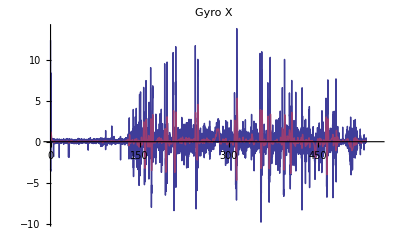

```mathematica
ListLinePlot[{RawGyroTable,FilteredGyroTable},PlotLabel->"Gyro X", PlotRange->{{0,550},All}]
```

# Rotation matrix

### Take a set of vectors and apply a rotation given the Euler angles

## Original vectors

```mathematica
v={{1,0,0},{0,1,0},{0,0,1}};
```

```mathematica
(*Graphics3D[Arrow[{{0,0,0},#}]&/@v,Axes->True,AxesLabel->{"x","y","z"}]*)
```

```mathematica
Graphics3D[{{Red,Arrow[{{0,0,0},v[[1]]}]},{Green,Arrow[{{0,0,0},v[[2]]}]},{Blue,Arrow[{{0,0,0},v[[3]]}]}},Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

## Apply a rotation using the following Euler angles

```mathematica
α=2.0 π/180.0;
β=3.0 π/180.0;
γ=50.0 π/180.0;
```

#### The rotation matrix is defines as follows, where the first rotation is in row (α), then pitch (β), and finally yaw (γ).

```mathematica
R=({{Cos[β]Cos[γ], Cos[β]Sin[γ], -Sin[β]}, {Sin[α]Sin[β]Cos[γ]-Cos[α]Sin[γ], Cos[α]Cos[γ]+Sin[α]Sin[β]Sin[γ], Sin[α]Cos[β]}, {Sin[α]Sin[γ]+Cos[α]Sin[β]Cos[γ], Cos[α]Sin[β]Sin[γ]-Sin[α]Cos[γ], Cos[α]Cos[β]}});
```

```mathematica
u=R.v;
```

```mathematica
(*Graphics3D[Arrow[{{0,0,0},#}]&/@u, Axes->True,AxesLabel->{"x","y","z"}]*)
```

```mathematica
Graphics3D[{{Red,Arrow[{{0,0,0},u[[1]]}]},{Green,Arrow[{{0,0,0},u[[2]]}]},{Blue,Arrow[{{0,0,0},u[[3]]}]}}, Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

## Apply a rotation to transform the u vector to the vector {{1,0,0},{0,1,0},{0,0,1}}

## Original vectors (u, the previously computed modified vector)

```mathematica
Rt=Transpose[R];
```

```mathematica
w=Rt.u;
```

```mathematica
(*Graphics3D[Arrow[{{0,0,0},#}]&/@w, Axes->True,AxesLabel->{"x","y","z"}]*)
```

```mathematica
Graphics3D[{{Red,Arrow[{{0,0,0},w[[1]]}]},{Green,Arrow[{{0,0,0},w[[2]]}]},{Blue,Arrow[{{0,0,0},w[[3]]}]}},Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

## The difference between the original and the transformed vectors is

```mathematica
d=Norm[w-v]
```

0.

```mathematica
Graphics3D[{Blue,Cylinder[],Red,Sphere[{0,0,2}],Black,Thick,Dashed,Line[{{-2,0,2},{2,0,2},{0,0,4},{-2,0,2}}],Yellow,Polygon[{{-3,-3,-2},{-3,3,-2},{3,3,-2},{3,-3,-2}}],Green,Opacity[.3],Cuboid[{-2,-2,-2},{2,2,-1}]}]
```

-Graphics3D-

```mathematica
Arrow[{{0,0,0},#}]&/@v
```

{Arrow[{{0,0,0},{1,0,0}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{0,0,1}}]}